## Rescuing the shower : change the DC coefs! (Problem 3.24)

```mathematica
Clear["Global`*"]
```

```mathematica
I0 =  IdentityMatrix[2]; TraditionalForm[I0]
```

(1 | 0
0 | 1)

```mathematica
G3 =  ({{1/(1+ s), (1/2)/(1+ τ s)}, {(1/2)/(1+  τ s), 1/(1+  s)}}) /. τ -> 1/2// Simplify
```

{{1/(1+s),1/(2+s)},{1/(2+s),1/(1+s)}}

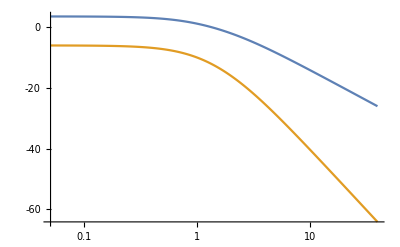

```mathematica
SingularValuePlot[G3]
```

Note the divergence of the condition number as s → ∞;  that' s ok because we control only up to a finite bandwith.
By contrast, a divergence at s → 0 is bad because we do care about DC response.

```mathematica
ComplexExpand[SingularValueList[G3/.s->ⅈ ω]]//FullSimplify
```

{ⅇ^(1/2 ⅈ Arg[1/((-2+ω (-3 ⅈ+ω)) (-2+Conjugate[ω] (3 ⅈ+Conjugate[ω])))]) √(1/(4+5 ω^2+ω^4)),ⅇ^(1/2 ⅈ Arg[((-3 ⅈ+2 ω) (3 ⅈ+2 Conjugate[ω]))/((-2+ω (-3 ⅈ+ω)) (-2+Conjugate[ω] (3 ⅈ+Conjugate[ω])))]) √((9+4 ω^2)/(4+5 ω^2+ω^4))}

```mathematica
G3inv = Inverse[G3] // Simplify;TraditionalForm[G3inv]
```

(((s+1) (s+2)^2)/(2 s+3) | -((s+1)^2 (s+2))/(2 s+3)
-((s+1)^2 (s+2))/(2 s+3) | ((s+1) (s+2)^2)/(2 s+3))

```mathematica
K3 =Ki3/(s(s+2)) I0 . G3inv /. Ki3-> 3;
```

```mathematica
K3a =((1+s/2)/(1+s/20))(3/(s(s+2)) )I0 . G3inv  // Simplify;
```

```mathematica
{MatrixForm[K3],MatrixForm[K3a]}
```

{((3 (1+s) (2+s))/(s (3+2 s)) | -(3 (1+s)^2)/(s (3+2 s))
-(3 (1+s)^2)/(s (3+2 s)) | (3 (1+s) (2+s))/(s (3+2 s))),((30 (1+s) (2+s)^2)/(s (20+s) (3+2 s)) | -(30 (1+s)^2 (2+s))/(s (20+s) (3+2 s))
-(30 (1+s)^2 (2+s))/(s (20+s) (3+2 s)) | (30 (1+s) (2+s)^2)/(s (20+s) (3+2 s)))}

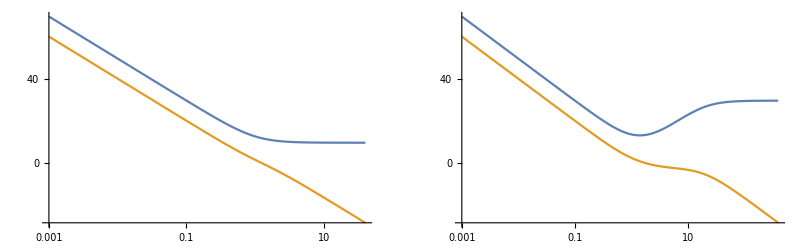

```mathematica
GraphicsRow[{SingularValuePlot[K3], SingularValuePlot[K3a]}]
```

In order for the controller to be "valid", it must be finite as  s → ∞ , else Mathematica complains.

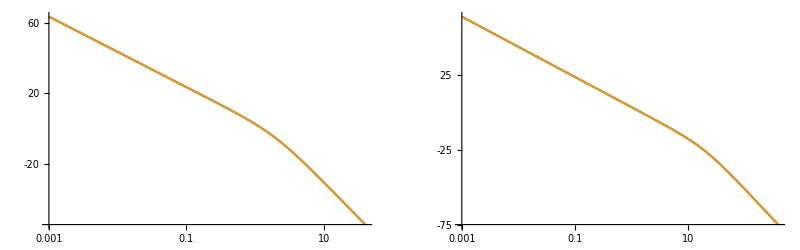

```mathematica
GraphicsRow[{SingularValuePlot[G3.K3], SingularValuePlot[G3.K3a]}]
```

```mathematica
S3 = Inverse[I0+ G3.K3] // Simplify
```

{{(s (2+s))/(3+2 s+s^2),0},{0,(s (2+s))/(3+2 s+s^2)}}

```mathematica
T3 = I0-S3 // Simplify
```

{{3/(3+2 s+s^2),0},{0,3/(3+2 s+s^2)}}

```mathematica
T3tf = TransferFunctionModel[T3,s]
```

3/(3+2 s+s^2)003/(3+2 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s22300331131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
u3tf = TransferFunctionModel[S3.K3,s]
```

(3 (1+s) (2+s)^2)/((3+2 s) (3+2 s+s^2))-(3 (1+s)^2 (2+s))/((3+2 s) (3+2 s+s^2))-(3 (1+s)^2 (2+s))/((3+2 s) (3+2 s+s^2))(3 (1+s) (2+s)^2)/((3+2 s) (3+2 s+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s223-3-3331FalseFalseFalseAutomaticNoneAutomatic

```mathematica
S3a =  Inverse[I0+ G3.K3a] // Simplify
```

{{(s (20+s))/(30+20 s+s^2),0},{0,(s (20+s))/(30+20 s+s^2)}}

```mathematica
T3a = I0-S3a // Simplify
```

{{30/(30+20 s+s^2),0},{0,30/(30+20 s+s^2)}}

```mathematica
T3atf =  TransferFunctionModel[T3a,s]
```

30/(30+20 s+s^2)0030/(30+20 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s223000303011301FalseFalseFalseAutomaticNoneAutomatic

```mathematica
u3atf =  TransferFunctionModel[S3a.K3a,s]
```

(30 (1+s) (2+s)^2)/((3+2 s) (30+20 s+s^2))-(30 (1+s)^2 (2+s))/((3+2 s) (30+20 s+s^2))-(30 (1+s)^2 (2+s))/((3+2 s) (30+20 s+s^2))(30 (1+s) (2+s)^2)/((3+2 s) (30+20 s+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s2230-30-303031FalseFalseFalseAutomaticNoneAutomatic

```mathematica
tmax = 3;
```

```mathematica
y3 = OutputResponse[T3tf,{UnitStep[t],(1/3)UnitStep[t]},{t,0,tmax}];
```

```mathematica
u3 = OutputResponse[u3tf,{UnitStep[t],(1/3)UnitStep[t]},{t,0,tmax}];
```

```mathematica
S3a = Inverse[I0+ G3.K3a];
T3a = I0-S3a;
```

```mathematica
y3a = OutputResponse[T3atf,{UnitStep[t],(1/3)UnitStep[t]},{t,0,tmax}];
u3a = OutputResponse[u3atf,{UnitStep[t],(1/3)UnitStep[t]},{t,0,tmax}];
```

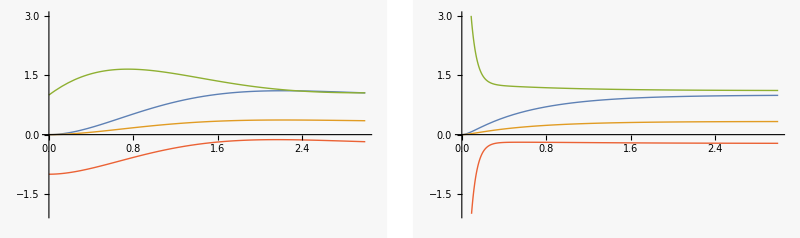

```mathematica
p3=Plot[{y3,u3},{t,0,tmax},PlotRange->{{0,tmax},{-2,3}}];p3a=Plot[{y3a,u3a},{t,0,tmax},PlotRange->{{0,tmax},{-2,3}}];
GraphicsRow[{p3,p3a}]
```

Export data

```mathematica
dt=0.01;
dat = Table[{t,y3[[1]],y3[[2]],u3[[1]],u3[[2]],y3a[[1]],y3a[[2]],u3a[[1]],u3a[[2]]},{t,0,tmax,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["MIMO-shower-problem_out.dat", dat];
*)
```